```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recuurent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 96, section 4.11*)
```

```mathematica
n0=6
```

6

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0,0,0,0,0,0}; s[2]={3,2,3,0,0,0,0,0,0}; s[3]={4,3,4,0,0,0,0,0,0};s[4]={5,4,5,0,0,0,0,0,0}; s[5]={6,5,6,0,0,0,0,0,0}; s[6]={1,6,1,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0,0,0},{0,1,2,0,0,0},{0,0,1,2,0,0},{0,0,0,1,2,0},{0,0,0,0,1,2},{2,0,0,0,0,1}}

```mathematica
MatrixForm[M]
```

(1 | 2 | 0 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 1 | 2 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 0 | 1 | 2
2 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

-63-6 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-1.},{x→0.-1.73205 ⅈ},{x→0.+1.73205 ⅈ},{x→2.-1.73205 ⅈ},{x→2.+1.73205 ⅈ},{x→3.}}

```mathematica
Clear[s]
```

```mathematica
s[1]={2,1,2}; s[2]={3,2,3}; s[3]={4,3,4};s[4]={5,4,5}; s[5]={6,5,6}; s[6]={1,6,1};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,6}]]
```

{2,1,2,3,2,3,4,3,4,5,4,5,6,5,6,1,6,1}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[10];
```

```mathematica
Length[aa]
```

1062882

```mathematica
bb=aa /. 1->{1,0}/. 2->{1,N[Sqrt[3]]}/2/. 3-> {-1,N[Sqrt[3]]}/2 /. 4->{-1,0}/. 5->{-1,-N[Sqrt[3]]}/2/. 6->{1,-N[Sqrt[3]]}/2;
```

```mathematica
gou=ListPlot[FoldList[Plus,{0,0},bb],PlotRange->All,PlotJoined->False,Axes->False,ColorFunction->Hue,PlotStyle->PointSize[0.001],Background->Black,ImageSize->2000];
```

```mathematica
Export["Gosper_substitution_level10_.jpg",gout]
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recuurent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 96, section 4.11*)
```

```mathematica
n0=6
```

6

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,1,2,0,0,0,0,0,0}; s[2]={3,2,3,0,0,0,0,0,0}; s[3]={4,3,4,0,0,0,0,0,0};s[4]={5,4,5,0,0,0,0,0,0}; s[5]={6,5,6,0,0,0,0,0,0}; s[6]={1,6,1,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,2,0,0,0,0},{0,1,2,0,0,0},{0,0,1,2,0,0},{0,0,0,1,2,0},{0,0,0,0,1,2},{2,0,0,0,0,1}}

```mathematica
MatrixForm[M]
```

(1 | 2 | 0 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 1 | 2 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 0 | 1 | 2
2 | 0 | 0 | 0 | 0 | 1)

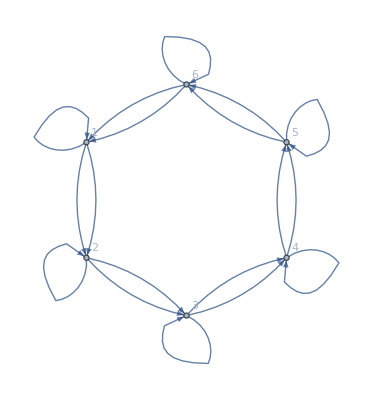

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
M1=Transpose[M]
```

{{1,0,0,0,0,2},{2,1,0,0,0,0},{0,2,1,0,0,0},{0,0,2,1,0,0},{0,0,0,2,1,0},{0,0,0,0,2,1}}

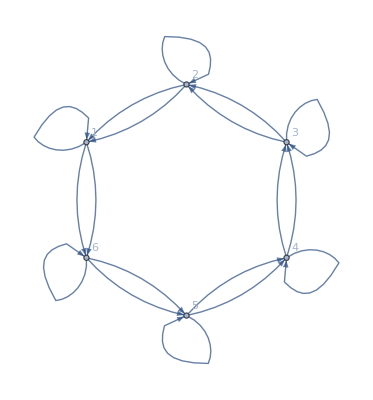

```mathematica
AdjacencyGraph[M1,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(*Isospectral*)
```

```mathematica
Eigenvalues[M]
```

{3,2+ⅈ √3,2-ⅈ √3,ⅈ √3,-ⅈ √3,-1}

```mathematica
Eigenvalues[M1]
```

{3,2+ⅈ √3,2-ⅈ √3,ⅈ √3,-ⅈ √3,-1}

```mathematica
(* make polynomial*)
```

```mathematica
Det[M1-x*IdentityMatrix[n0]]
```

-63-6 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M1-x*IdentityMatrix[n0]]==0,x]
```

{{x→-1.},{x→0.-1.73205 ⅈ},{x→0.+1.73205 ⅈ},{x→2.-1.73205 ⅈ},{x→2.+1.73205 ⅈ},{x→3.}}

```mathematica
Clear[s]
{{1,0,0,0,0,2},{2,1,0,0,0,0},{0,2,1,0,0,0},{0,0,2,1,0,0},{0,0,0,2,1,0},{0,0,0,0,2,1}};
```

```mathematica
s[1]={6,1,6};s[2]={1,2,1};s[3]={2,3,2};s[4]={3,4,3};s[5]={4,5,4};s[6]={5,6,5};
```

```mathematica
(*original substitution:s[1]={2,1,2}; s[2]={3,2,3}; s[3]={4,3,4};s[4]={5,4,5}; s[5]={6,5,6}; s[6]={1,6,1};*)
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,6}]]
```

{6,1,6,1,2,1,2,3,2,3,4,3,4,5,4,5,6,5}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[10];
```

```mathematica
Length[aa]
```

1062882

```mathematica
bb=aa /. 1->{1,0}/. 2->{1,N[Sqrt[3]]}/2/. 3-> {-1,N[Sqrt[3]]}/2 /. 4->{-1,0}/. 5->{-1,-N[Sqrt[3]]}/2/. 6->{1,-N[Sqrt[3]]}/2;
```

```mathematica
gout=ListPlot[FoldList[Plus,{0,0},bb],PlotRange->All,PlotJoined->False,Axes->False,ColorFunction->Hue,PlotStyle->PointSize[0.001],Background->Black,ImageSize->2000];
Export["Gosper_transpose_substitution_level10_isospectral.jpg",gout]
```

Gosper_transpose_substitution_level10_isospectral.jpg

```mathematica
(*end*)
```